## Test power mode

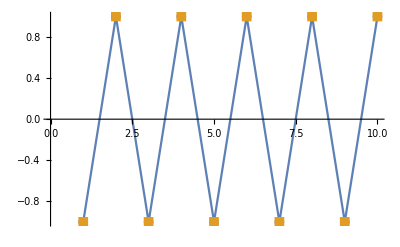

```mathematica
fp[k_]:=(-1)^k;
t=Table[{i,fp[i]},{i,1,10,1}];
t2=Table[{i,fp[i]},{i,1,10,1}];
ListPlot[{t,t2},Joined->{True,False},PlotMarkers->{Automatic, Medium}]
```